```mathematica
UnitTest[ description_, val_, expr_ ] := 
	If [val == expr, "ok", StringJoin[ "ERROR: GOT UNEXPECTED VALUE ", ToString[expr], " INSTEAD OF ", ToString[val]]]
```

{{2,150},{3,188},{4,246},{5,282},{6,362},{7,436},{8,540},{9,632},{10,750},{11,870},{12,990},{13,1115},{14,1270},{15,1440},{16,1608},{17,1780},{18,1950}}

{{150,2},{188,3},{246,4},{282,5},{362,6},{436,7},{540,8},{632,9},{750,10},{870,11},{990,12},{1115,13},{1270,14},{1440,15},{1608,16},{1780,17},{1950,18}}

93.8676+16.2393 x+4.86365 x^2

100+15 x+5 x^2

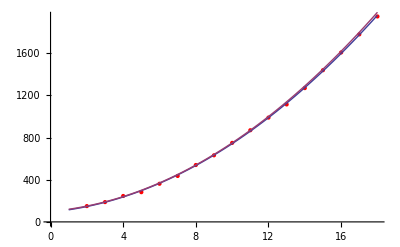

```mathematica
(* Curve fitting to find exp growth as a function of time *)
data = { (* level,game-time (seconds) *)
{2,150},
{3,188},
{4,246},
{5,282},
{6,362},
{7,436},
{8,540},
{9,632},
{10,750},
{11,870},
{12,990},
{13,1115},
{14,1270},
{15,1440},
{16,1608},
{17,1780},
{18,1950}
}
data2 = {#[[2]],#[[1]]}& /@ data
parabola = Fit[data, {1,x,x^2}, x]
para2 = 100+15x+5 x^2
Show[ListPlot[data,PlotStyle->Red],Plot[{parabola,para2},{x,1,18}]]
(*
parabola2 = Fit[data2, {1,x, x^2}, x]
parabola3 =0.72 +0.0145 x-3.0*^-6 x^2
Show[ListPlot[data2,PlotStyle->Red],Plot[{parabola3,parabola3},{x,150,2000}]]

levelAt[t_/; t > 100] := 1/10 (-15+Sqrt[5] Sqrt[-355+4 t])
levelAt[t_]:=1
*)

timeAt[lv_] := 100+15lv+5 lv^2
timeAt[1] := 0
```

LV | Gold
1 | 475
2 | 967.
3 | 1163.
4 | 1526.
5 | 1880.
6 | 2284.
7 | 2834.
8 | 3406.
9 | 4004.
10 | 4753.
11 | 5559.
12 | 6366.
13 | 7366.
14 | 8365.
15 | 9430.
16 | 10672.
17 | 11953.
18 | 13273.

840.777+38.4742 x^2

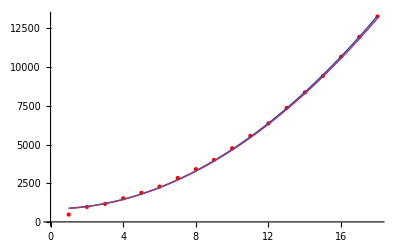

```mathematica
(* Exact gold generation over time and approximate formula *)
wavesPerSecond = 1/30;
siege2Wave = (35*60) wavesPerSecond;
upgradeCycle = 180; (*seconds*)
firstWaveAt = 90; (*seconds*)

cycle[t_] := Floor[t / upgradeCycle]

minionCaster[t_] := 16.5 + 0.5 cycle[t]
minionMelee[t_] := 22.5 + 0.5 cycle[t]
minionSiege[t_] := 27 + 1 cycle[t]

waveGold[t_,w_Integer/; w ≤ 0] := 0
waveGold[t_,w_Integer] := waveGold[t-30,w-1] + 3 minionCaster[t] + 3 minionMelee[t] + Boole@(Mod[w,If[w ≥ siege2Wave,2,3]]==0)minionSiege[t]

minionGoldAt[t_] := waveGold[t,Floor[(t-60) wavesPerSecond]]
(* TODO: make sure this is right *)
Clear[passiveGoldAt]
passiveGoldAt[t_/; t < firstWaveAt] := 0
passiveGoldAt[t_] := ((t-firstWaveAt)/10)*19 (*summoner's rift*)
exactGoldAtTime[t_] := minionGoldAt[t] + passiveGoldAt[t] + 475

data = {#,exactGoldAtTime[timeAt[#]]}& /@ Range[1,18];
Join[{{"LV","Gold"}},data] // TableForm
parabola = Fit[data, {1, x^2}, x]
Show[ListPlot[data,PlotStyle->Red],Plot[{parabola,840+38 x^2},{x,1,18}]]

goldAtLV[lv_]:= 840 + 38 lv^2
```

```mathematica
armor[ppen_] := (100/(100+(xArmor*ppen)))


(*
#define AS_OFFSET         (-0.04)
perlvAS := 0.0322f
baseAS := (0.625/(1+AS_OFFSET))
	float level = (float)(LV - 1);
	float bonus = PERCENT(GEAR);

	return min(2.5f, AS_BASE * (1.0f + (AS_LVPER*level) + bonus));
*)
             (*1 2 3 4 5 6 7 8 9 10 11 12 13 14 15 16 17 18 *)
upgradepath = {3,1,2,2,2,4,2,2,3,3, 4, 3, 3, 1, 1, 4, 1, 1 };
abilityRank = Module[{r={0,0,0,0},n=#}, 
	While[n>0, r⟦upgradepath⟦n⟧⟧++; n--]; r]&/@Range[1,Length[upgradepath]
	];
sheenproc[] := {xBaseAttack*xSpellBlade, 2, 1}

hitenStyle = {
	{15,15,6},
	{30,15,6},
	{45,15,6},
	{60,15,6},
	{75,15,6}
	};
bladeSurge[mitigation_]:= Module[{a={
	{20,14,1}, 
	{50,12,1},
	{80,10,1},
	{110,8,1},
	{140,6,1}}},
	a⟦All,1⟧ = mitigation*(#+xAttack)&/@a⟦All,1⟧; a]

equilibriumStrike[mitigation_] := Module[{a={
	{80,8,1},
	{130,8,1},
	{180,8,1},
	{230,8,1},
	{280,8,1}
	}},
	a⟦All,1⟧ = mitigation * (#+(xAbilityPower/2))&/@a⟦All,1⟧; a]

transcendentBlades[mitigation_] := Module[{a={
	{80,70,4},
	{120,60,4},
	{160,50,4}
	}},
	a⟦All,1⟧ = mitigation * (#+(xAbilityPower/2)+(xAttack*6/10))&/@a⟦All,1⟧; a]

Clear[abilities,dps]
priority = {2,4,3,1}
abilities[level_Integer/;level < 1,_] := {}
abilities[level_Integer, mitigation_] := Module[{xs,ys},
	xs={bladeSurge[mitigation], hitenStyle, equilibriumStrike[mitigation], transcendentBlades[mitigation]};
	ys=MapIndexed[If[#1>0,First@xs⟦#2,#1⟧, Undefined]&, abilityRank⟦level⟧];
	Select[ys⟦priority⟧, !MatchQ[#,Undefined]&]
]

autoAttackDmg[resist_] := resist * xAttack * xCriticalStrike

applyDoT[{{dmg_,cooldown_,duration_},0}] := 0
applyDoT[{{dmg_,cooldown_,duration_},timer_}] := If[cooldown-timer < duration, dmg, 0]

useAbility[as_,cs_,elapsed_,spellblade_]:= Module[{cs2,pos,i,dmg},
	cs2=Max[0,#-elapsed]&/@cs;
	pos=Position[cs2, 0]; 
	If [Length[pos] ≠ 0, i=First@First@pos; cs2⟦i⟧ = as⟦i⟧⟦2⟧];
	dmg=Total[applyDoT/@Thread[{as,cs2}]] + spellblade;
	{cs2, dmg}
	]

simstep[{spell_, aa_, spd_, spellblade_}, {health_, cooldowns_, result_}] := With[
		{x=useAbility[spell,cooldowns,1/spd,spellblade]}, 
		{health-(x⟦2⟧+aa), x⟦1⟧, result + {1/spd,x⟦2⟧,aa}}
	]

siminit[level_, enemy_, armorReduction_] := Module[{mitigation,spell},
	mitigation=armor[armorReduction] //. enemy;
	spell=abilities[level, mitigation];
	{{spell, autoAttackDmg[mitigation], xAttackSpeed, xSpellBlade * xBaseAttack}, {xHealth/.enemy, ConstantArray[0,Length[spell]], {0,0,0}}}]

tick[{ctx_, {health_/; health ≤ 0, _, result_}}] := result⟦1⟧
tick[{ctx_, {health_?NumericQ, cooldowns_, result_}}] := tick[{ctx,simstep[ctx, {health, cooldowns, result}]}]

combatSim[level_Integer/; level < 1, enemy_, armorReduction_] := 0
combatSim[level_Integer, enemy_, armorReduction_] := tick@siminit[level, enemy, armorReduction]

abilities[9,1]
abilities[16,1]
st1 = {xBaseAttack :> 100, xAttack :> 100, xCriticalStrike :> 1, xAttackSpeed -> 1.0, xSpellBlade :> 0, xBaseAttack :> 50, xAbilityPower :> 0}
combatSim[3, {xHealth :> 1000, xArmor :> 10}, 1.0] //. st1
combatSim[3, {xHealth :> 1000, xArmor :> 10}, 1.0] //. {xBaseAttack :> 100, xBaseAttack :> 50, xAttack :> 100, xCriticalStrike :> 1, xAttackSpeed -> 1.0, xSpellBlade :> 1, xAbilityPower :> 0}
(*{7,451.81818181818187,636.3636363636363}*)
{ctx1,ctx2} = siminit[16, {xHealth :> 1000, xArmor :> 10}, 1.0] //. st1
ctx2 = simstep[ctx1,ctx2]
ctx2 = simstep[ctx1,ctx2]
ctx2 = simstep[ctx1,ctx2]
ctx2 = simstep[ctx1,ctx2]
```

{2,4,3,1}

{{75,15,6},{80+xAbilityPower/2+(3 xAttack)/5,70,4},{130+xAbilityPower/2,8,1},{20+xAttack,14,1}}

{{75,15,6},{160+xAbilityPower/2+(3 xAttack)/5,50,4},{280+xAbilityPower/2,8,1},{80+xAttack,10,1}}

{xBaseAttack:>100,xAttack:>100,xCriticalStrike:>1,xAttackSpeed→1.,xSpellBlade:>0,xBaseAttack:>50,xAbilityPower:>0}

9.

4.

{{{{75,15,6},{200.,50,4},{254.545,8,1},{163.636,10,1}},90.9091,1.,0},{1000,{0,0,0,0},{0,0,0}}}

{834.091,{15,0,0,0},{1.,75,90.9091}}

{468.182,{14.,50,0,0},{2.,350.,181.818}}

{-152.273,{13.,49.,8,0},{3.,879.545,272.727}}

{-681.818,{12.,48.,7.,10},{4.,1318.18,363.636}}

```mathematica
gold := goldAtLV[lv]

costAttack = 36
costHealth = 2.64
costArmor = 20
costAbilityPower = 21.75
costCriticalChance = 50*100
costAttackSpeed = 33.33*100

championIrelia = { 
	cHealthBase -> 456, cHealthLv -> 90, 
	cAttackBase -> 56, cAttackLv -> 3.3,
	cArmorBase -> 15, cArmorLv -> 3.75,
	cAttackSpeedBase :> 0.625, cAttackSpeedDelay :> −0.06, cAttackSpeedLv -> 0.0322 };

stats[lv_, champion_] := With[{
	baseHP = cHealthBase + cHealthLv(lv-1),
	baseAD = cAttackBase + cAttackLv(lv-1),
	baseArmor = cArmorBase + cArmorLv(lv-1),
	crit = With[{ξ=gCriticalChance/costCriticalChance}, 1 + (1 *Min[1,ξ])],
	aspd = With[{ξ=gAttackSpeed/costAttackSpeed}, Min[2+1/2, (cAttackSpeedBase/(1+cAttackSpeedDelay)) * (1 + (cAttackSpeedLv*(lv-1)) + ξ)]]
	},
	
	{xBaseAttack     :> baseAD, 
	 xAttack         :> baseAD + (gAttack/costAttack), 
	 xHealth         :> baseHP +(gHealth/costHealth), 
	 xArmor          :> baseArmor + (gArmor/costArmor),
	 xAbilityPower   :> (gAbilityPower/costAbilityPower),
     xCriticalStrike :> crit, 
	 xAttackSpeed    :> aspd} //. champion
]

statsym = {gAttack, gCriticalChance, gAttackSpeed, gHealth, gArmor, gAbilityPower, xSpellBlade};
gdistro[xs__] := Map[# -> gold 1/Length[{xs}]&, {xs}] ~Join~ gdistro[]
gdistro[] := # -> 0& /@ statsym
evendistro = gdistro@@statsym;

metric[lv_Integer, me_, him_, peelduration_, armorReduction_] := Module[
	{killHim,killMe},
	killHim= combatSim[lv, him, armorReduction] //. me;
	killMe = combatSim[lv, me, armorReduction] //. him;
	killHim
(*(killMe+peelduration) - *)
]
metric[lv_/;lv<1, _, _, _] := 0
metric[lv_, champ_, b_, c_] := metric[Floor[lv], stats[Floor[lv], champ], stats[Floor[lv], champ] /. evendistro, b, c]
iTrinity     = {3, {10,50,5,1,0,0.10}}
iZeal        = {375,{0,0,0,0,0.02,0.08}}
iDagger      = {400,{0,0,0,0,0,0.12}}
iBrawlGlove  = {400,{0,0,0,0,0.08,0}}
iSheen       = {1200,{0,0,25,1,0,0}}
iPhage       = {490,{10,20,0,0,0,0}}
iRubyCrystal = {475,{0,180,0,0,0,0}}
iLongSword   = {360,{10,0,0,0,0,0}}
buildPath = {iRubyCrystal,iLongSword,iPhage,iDagger,iBrawlGlove,iZeal,iSheen,iTrinity}

trinityforce[gold_Integer] := With[{x=Reverse[Select[FoldList[#1+#2&, {0,{0,0,0,0,0,0}}, buildPath], #⟦1⟧ < gold&]]⟦1,2⟧},
	{gAttack -> x⟦1⟧*costAttack, gHealth -> x⟦2⟧*costHealth, 
	 gAbilityPower -> x⟦3⟧*costAbilityPower, 
	 xSpellBlade -> x⟦4⟧,
	 gCriticalChance -> x⟦5⟧*costCriticalChance,
	 gAttackSpeed -> x⟦6⟧*costAttackSpeed
	} ~Join~ gdistro[]]

trinityforce[4000]
1.0 * xAttackSpeed /. Block[{lv=2}, stats[lv, championIrelia] //. gdistro[gAttackSpeed]]
Block[{lv=5}, metric[lv, championIrelia, 0, 1] //. gdistro[gAttackSpeed,gHealth,gAttack]]
Block[{lv=5}, metric[lv, championIrelia, 0, 1] //. gdistro[gAttack]]
Block[{lv=18}, metric[lv, championIrelia, 0, 1] //. trinityforce[gold]]
```

36

2.64

20

21.75

5000

3333.

{3,{10,50,5,1,0,0.1}}

{375,{0,0,0,0,0.02,0.08}}

{400,{0,0,0,0,0,0.12}}

{400,{0,0,0,0,0.08,0}}

{1200,{0,0,25,1,0,0}}

{490,{10,20,0,0,0,0}}

{475,{0,180,0,0,0,0}}

{360,{10,0,0,0,0,0}}

{{475,{0,180,0,0,0,0}},{360,{10,0,0,0,0,0}},{490,{10,20,0,0,0,0}},{400,{0,0,0,0,0,0.12}},{400,{0,0,0,0,0.08,0}},{375,{0,0,0,0,0.02,0.08}},{1200,{0,0,25,1,0,0}},{3,{10,50,5,1,0,0.1}}}

{gAttack→1080,gHealth→660.,gAbilityPower→652.5,xSpellBlade→2,gCriticalChance→500.,gAttackSpeed→999.9,gAttack→0,gCriticalChance→0,gAttackSpeed→0,gHealth→0,gArmor→0,gAbilityPower→0,xSpellBlade→0}

0.884195

10.3501

9.32672

4.8847

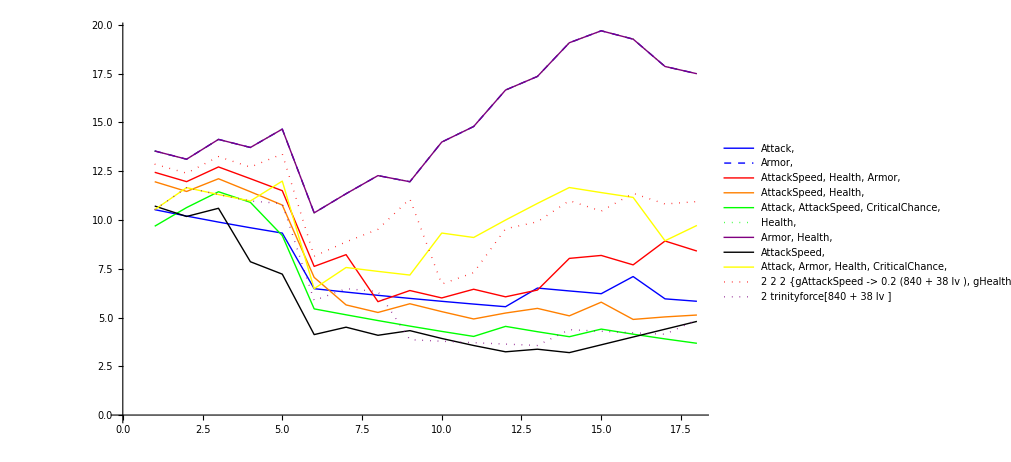

13152

```mathematica
dataset = { 
	  {gAttack},
	  {gArmor},
	  {gAttackSpeed, gHealth, gArmor},
	  {gAttackSpeed, gHealth},
	  {gAttack, gAttackSpeed, gCriticalChance},
	  {gHealth},
	  {gArmor, gHealth},
	  {gAttackSpeed},
	  {gAttack, gArmor, gHealth, gCriticalChance}
	};

dataset2 := {{gAttackSpeed -> gold*0.20, gHealth -> gold*0.40, gArmor -> gold*0.40}, trinityforce[gold]}

colors = {Blue,
		  Directive[Dashed,Blue,Thick],
		  Red,
		  Directive[Orange],
		  Green, 
	      Directive[Dotted,Green,Thick],
		  Directive[Purple],
		  Black,
		  Directive[Yellow],
		  Directive[Dotted,Red,Thick],
		  Directive[Dotted,Purple,Thick]
};
label[x_] := StringDrop[ToString[x],1]
label[xs_List] := StringJoin[({label[#], ", "}&)/@xs]

Clear[measure]
measure[level_] := Block[{lv=level},(metric[lv, championIrelia, 0, 1] //. #&)/@Join[
	gdistro@@#&/@dataset, 
	#~Join~gdistro[]&/@dataset2]];
(*
Plot[measure[lv], {lv,0,18}, PlotLegends->label/@dataset, PlotStyle-> colors]
*)
matrix = Thread[{#,measure[#]}]&/@Range[1, 18];
ListLinePlot[Transpose@matrix, PlotLegends -> Join[label/@dataset, ToString/@dataset2], PlotStyle-> colors]
goldAtLV[18]
```

```mathematica
NMaximize[{Block[{lv=#},metric[lv, championIrelia, 0, 0.94]], {Total[statsym] == 1}, Thread[statsym ≥ -0.001], Thread[statsym ≤ 1]}, statsym, AccuracyGoal -> 2, PrecisionGoal -> 2]& /@ {1,6,11,16,18}
```

{{4.27499,{gAttack→0.0642178,gCriticalChance→0.0113799,gAttackSpeed→0.150488,gHealth→0.672991,gArmor→0.0340201,gAbilityPower→0.066903}},{5.30909,{gAttack→0.0752857,gCriticalChance→0.0127408,gAttackSpeed→0.0358714,gHealth→0.771508,gArmor→0.105642,gAbilityPower→-0.00104812}},{0.906504,{gAttack→-0.000999999,gCriticalChance→-0.000999999,gAttackSpeed→0.645598,gHealth→0.358402,gArmor→-0.000999999,gAbilityPower→-0.000999989}},{2.31331,{gAttack→-0.001,gCriticalChance→-0.001,gAttackSpeed→0.542716,gHealth→0.461284,gArmor→-0.001,gAbilityPower→-0.000999987}},{2.98479,{gAttack→0.00187079,gCriticalChance→0.00645131,gAttackSpeed→0.603907,gHealth→0.165197,gArmor→0.213893,gAbilityPower→0.00868097}}}

```mathematica
trinityforce[goldAtLV[1]]
{goldAtLV[1],goldAtLV[1]/2/costHealth,goldAtLV[1]*1.0/2/costAttack}
trinityforce[goldAtLV[4]]
trinityforce[goldAtLV[6]]
trinityforce[goldAtLV[8]]
trinityforce[goldAtLV[9]]
```

{gAttack→0,gHealth→0.,gAbilityPower→0.,xSpellBlade→0,gCriticalChance→0,gAttackSpeed→0.,gAttack→0,gCriticalChance→0,gAttackSpeed→0,gHealth→0,gArmor→0,gAbilityPower→0,xSpellBlade→0}

{878,166.288,12.1944}

{gAttack→0,gHealth→0.,gAbilityPower→543.75,xSpellBlade→1,gCriticalChance→0,gAttackSpeed→0.,gAttack→0,gCriticalChance→0,gAttackSpeed→0,gHealth→0,gArmor→0,gAbilityPower→0,xSpellBlade→0}

{gAttack→360,gHealth→475.2,gAbilityPower→543.75,xSpellBlade→1,gCriticalChance→0,gAttackSpeed→0.,gAttack→0,gCriticalChance→0,gAttackSpeed→0,gHealth→0,gArmor→0,gAbilityPower→0,xSpellBlade→0}

{gAttack→720,gHealth→528.,gAbilityPower→543.75,xSpellBlade→1,gCriticalChance→0,gAttackSpeed→399.96,gAttack→0,gCriticalChance→0,gAttackSpeed→0,gHealth→0,gArmor→0,gAbilityPower→0,xSpellBlade→0}

{gAttack→1080,gHealth→660.,gAbilityPower→652.5,xSpellBlade→2,gCriticalChance→500.,gAttackSpeed→999.9,gAttack→0,gCriticalChance→0,gAttackSpeed→0,gHealth→0,gArmor→0,gAbilityPower→0,xSpellBlade→0}